```mathematica
SetDirectory[FileNameJoin[{ParentDirectory[NotebookDirectory[]],"RABBIT_Packages"}]];
Needs["MagicGeneDropping`"]
SetDirectory[NotebookDirectory[]];
```

```mathematica
(*****************************************************************************************************************)
```

```mathematica
Options[simPedigreeInfor]
Options[magicGeneDropping]
```

{sampleSize→100,sampleGender→Hermaphrodite,funnelFunction→(RandomSample[#1]&),outputFileID→}

{founderAllelicError→0.005,offspringAllelicError→0.005,isFounderInbred→True,dropMonomorphic→False,interferenceStrength→0,isObligate→False,phredQualScore→30,founderGenotypeMissing→0,founderReadDepth→0,offspringGenotypeMissing→0,offspringReadDepth→0,depthDistribution→NegativeBinomial-1,outputFileID→,isPrintTimeElapsed→True}

Simulating pedinfor from pedigree!

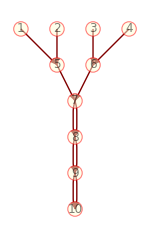

```mathematica
founderhaplofile="Arabidopsis_MAGIC_19FounderHaplo.csv";
outputid="Example";
size=100;
Switch[RandomChoice[Range[3]],
1,
Print["Simulating pedinfor from string code!"];
popcode="4wayril-self3";
simpedinforfile=simPedigreeInfor[popcode,sampleSize->size,outputFileID->outputid],
2,
Print["Simulating pedinfor from mating schemes!"];
nfounder=4;
matescheme={"Pairing","Pairing","Selfing","Selfing","Selfing"};
simpedinforfile=simPedigreeInfor[nfounder,matescheme,sampleSize->size,outputFileID->outputid],
3,
Print["Simulating pedinfor from pedigree!"];
pedigree0={{"Generation","MemberID","Female=1/Male=2/Hermaphrodite=0",{"MotherID","FatherID"}},{0,1,0,{0,0}},{0,2,0,{0,0}},{0,3,0,{0,0}},{0,4,0,{0,0}},{1,5,0,{1,2}},{1,6,0,{3,4}},{2,7,0,{5,6}},{3,8,0,{7,7}},{4,9,0,{8,8}},{5,10,0,{9,9}}};
simpedinforfile=simPedigreeInfor[pedigree0,sampleSize->size,outputFileID->outputid];
];
(*pedigree===pedigree0*)
pedigree=splitPedigreeInfor[Import[simpedinforfile]][[2]];
pedigreePlot[pedigree,ImageSize->150]
```

```mathematica
datafiles=magicGeneDropping[founderhaplofile,simpedinforfile,dropMonomorphic->True,outputFileID->outputid,isFounderInbred->True,founderGenotypeMissing->0.1,founderReadDepth->0,offspringGenotypeMissing->0.5,offspringReadDepth->0]
```

magicGeneDropping. Start date = Mon 2 Jul 2018 12:17:55

Time elapsed = 0. Seconds. 	Start simulating offspring genomes in terms of FGL lists.

Time elapsed = 4.8 Seconds. 	Start dropping founder alleles on the offspring FGL lists.

Time elapsed = 10.2 Seconds. 	Start simulating allelic errors in founders and offspring.

The realized fraction of missing genotypes in founders: 0.097

The realized fraction of missing genotypes in offspring: 0.498

Saving true values and simulated data. Mon 2 Jul 2018 12:18:06
	True FGL | Example_TrueValues_Fgl.txt
True FGL diplotype | Example_TrueValues_FglDiplotype.csv
True diplotype | Example_TrueValues_Diplotype.csv
Observed genotype | Example_ObservedGenotype.csv

Done! Finished date =Mon 2 Jul 2018 12:18:07. 	Time elapsed = 11.9 Seconds.

{Example_TrueValues_Fgl.txt,Example_TrueValues_FglDiplotype.csv,Example_TrueValues_Diplotype.csv,Example_ObservedGenotype.csv}

```mathematica
(*****************************************************************************************************************)
```